### 4. Starobinsky Potential

### Below is the equation for the Starobinsky potential found on Valentino’s Starobinsky Inflationary Potential paper as eqn 2.4,

→ V(ϕ) = V_0( 1-e^(-√(2/3)ϕ/M_P))^2

```mathematica
(* Where Mp = the Planck mass *)
```

### Then recall Wiltshire eqn 3.56,

1/𝒩 d/dt((ϕ̇)/𝒩 )+3(ȧ)/(a(𝒩)^2)ϕ̇+1/2(dV/dϕ)=0

### Let N = 1 and make the substitutions using Valentino’s derivation for the derivative of the Starobinsky Potential with respect to ϕ,

d/dt(ϕ̇ )+3(ȧ)/a ϕ̇+1/2 d/dϕ(V_0( 1-e^(-√(2/3)ϕ/M_P))^2)=0 

(ϕ^(..) )+3(ȧ)/a ϕ̇+1/2(2 √(2/3)V_0/M_P(1-e^(-√(2/3)ϕ/M_P))e^(-√(2/3)ϕ/M_P)=0

(ϕ^(..) )+3(ȧ)/a ϕ̇+(√(2/3)V_0/M_P(1-e^(-√(2/3)ϕ/M_P))e^(-√(2/3)ϕ/M_P)=0

### For the second diff eq, we use Wiltshire eqn 3.54 and solve using N = 1, k = 0, and eqn 5,

H=1/2(-OverDot[aa]^2/𝒩^2+(a^3(ϕ̇)^2)/𝒩^2-ka+a^3 V)=0
1/2(-OverDot[aa]^2+a^3(ϕ̇)^2-ka+a^3 V)=0
-(ȧ)^2+a^2(ϕ̇)^2+a^2(V_0( 1-e^(-√(2/3)ϕ/M_P))^2)=0

### Now we can try to use NDSolve to solve the eqns as we’ve done above,

```mathematica
Subscript[M, P]=1   (* natural units *)
```

1

```mathematica
star=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+(√(2/3)*(1/Subscript[M, P])*(1-e^(-√(2/3)*(ϕ[t]/Subscript[M, P])))*e^(-√(2/3)(ϕ[t]/Subscript[M, P])))==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2*(1-e^(-√(2/3)*(ϕ[t]/Subscript[M, P])))^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.001.

NDSolve[{√(2/3) e^(-√(2/3) ϕ[t]) (1-e^(-√(2/3) ϕ[t]))+(3 a'[t] ϕ'[t])/a[t]+ϕ''[t]==0,(1-e^(-√(2/3) ϕ[t]))^2 a[t]^2-a'[t]^2+a[t]^2 ϕ'[t]^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]

```mathematica
Plot[Evaluate[{a[t],ϕ[t]}],{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

-Graphics-

```mathematica
(* This is not working so I'm going to try to simplify the potential (eqn 5) using the approximation given in the Planck 2018 Results Paper where 
V ∝ ϕ^p *)
```

### ***Starobinsky Approximation: I’m going to use the approximation V ~ (1-e^-ϕ)^2 just to make it easier,

### Below is the equation for the Starobinsky potential (found on Wiki and similarly on Valentino’s Starobinsky Inflationary Potential paper) which is in an inflationary model of the form R + R/(6M^2) found in Table 5 of the Planck 2018 Results paper,

### → V(ϕ) = Λ^4( 1-e^(-√(2/3)ϕ/M_P))^2

### Using the approximation for V given in the Planck paper of V ∝ ϕ^p , we can simplify the equation easier and hopefully get an actual plot for the functions,

→ V(ϕ) = ( 1-e^-ϕ)^2

### Using Wiltshire’s eqn 3.56 and simplifying,

d/dt(ϕ̇ )+3(ȧ)/a ϕ̇+1/2(dV/dϕ)=0
ϕ^(..) +3(ȧ)/a ϕ̇+1/2 d/dϕ[(1-e^-ϕ)^2]=0
ϕ^(..) +3(ȧ)/a ϕ̇+e^(-2ϕ)(e^ϕ-1)=0
ϕ^(..) +3(ȧ)/a ϕ̇+e^-ϕ-e^(-2ϕ)=0

#### Then using Wiltshire’s eqn 3.54 and simplifying,

-(ȧ)^2+a^2(ϕ̇)^2+a^2[(1-e^-ϕ)^2]=0   <--- star2 uses this version of the equation
-(ȧ)^2+a^2(ϕ̇)^2+a^2(1-2 e^-ϕ+e^(-2ϕ))=0
-(ȧ)^2+a^2(ϕ̇)^2+a^2-2 a^2 e^-ϕ+a^2 e^(-2ϕ)=0 
(-(ȧ)^2)/a^2+(ϕ̇)^2-2 e^-ϕ+e^(-2ϕ)=0              <--- star3 uses this version of the equation

```mathematica
star2=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+Exp[-ϕ[t]]-Exp[-2*ϕ[t]]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2*((1-Exp[-ϕ[t]])^2)==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199987, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {-2.99953} lies outside the range of data in the interpolating function. Extrapolation will be used.

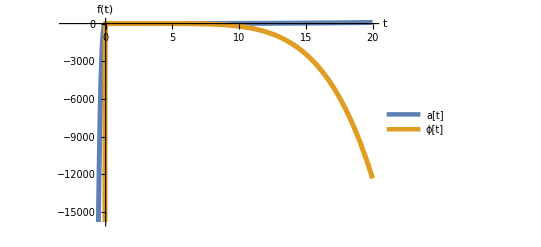

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.star2],{t,-3,20},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

This graph isn’t too ugly or weird. The only strange thing is that a(t) is 0 pretty much all the time for t>0 . Below, I plotted the same thing but with the positive ϕ approximation for V,  i.e.  V ~ (1-e^(+ϕ))^2 .

### ***Starobinsky Re-do: I’m going to use the approximation V ~ (1-e^(+ϕ))^2 just to flip the potential over the x-axis,

ϕ^(..) +3(ȧ)/a ϕ̇+1/2 d/dϕ[(1-e^ϕ)^2]=0
ϕ^(..) +3(ȧ)/a ϕ̇-e^ϕ+e^(2ϕ)=0

### Now for a[t] (eqn 3.56),

-(ȧ)^2+a^2(ϕ̇)^2+a^2[(1-e^ϕ)^2]=0 
-(ȧ)^2+a^2(ϕ̇)^2+a^2(1-2 e^ϕ+e^(2ϕ))=0

```mathematica
star4=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]-Exp[ϕ[t]]+Exp[2*ϕ[t]]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2*((1-Exp[-ϕ[t]])^2)==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199993, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {-4.99929} lies outside the range of data in the interpolating function. Extrapolation will be used.

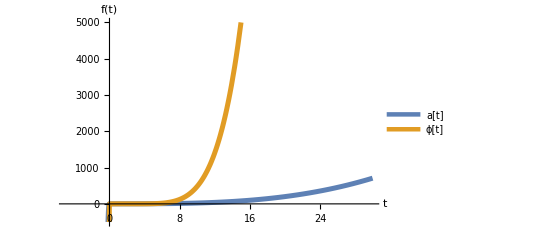

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.star4],{t,-5,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotRange->{-500,5000},PlotStyle->{Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

```mathematica
(* Notice, ϕ[t] increases much more rapidly than a[t] so I plotted a[t] alone below just so I could see what it's doing *)
```

InterpolatingFunction::dmval: Input value {-4.99908} lies outside the range of data in the interpolating function. Extrapolation will be used.

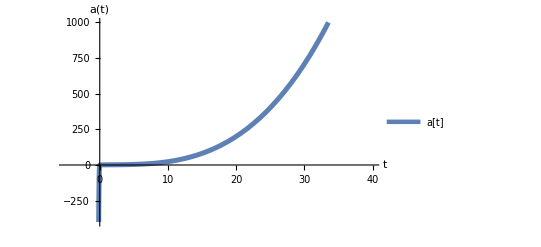

```mathematica
Plot[{a[t]}/.star4,{t,-5,40},PlotRange->{-400,1000},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotStyle->{Thickness[0.009]},PlotLegends->{"a[t]"}]
```

```mathematica
(* Above is just a[t] on its own and it is increasing exponentially, just much much slower than ϕ[t] *)
(* Before I plotted a[t] on its own (above) and changed the PlotRange for the a[t] and ϕ[t] graph, I thought a[t] was stuck at 0 for t > 0 but it's  not, just relatively slower increase *)
```

### Finally, I’m going to make a parametric plot for a[t] and ϕ[t],

InterpolatingFunction::dmval: Input value {0.002004} lies outside the range of data in the interpolating function. Extrapolation will be used.

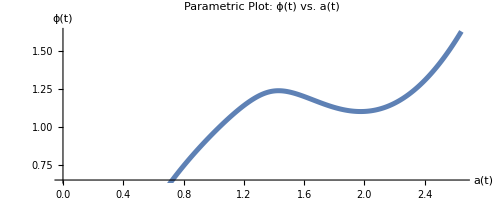

```mathematica
ParametricPlot[Evaluate[{a[t],ϕ[t]+1}/.star4],{t,0.002,4},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,PlotStyle->{Thickness[0.009]},PlotLabel->"Parametric Plot: ϕ(t) vs. a(t)"]
```

### Now, I’m going to just plot the Starobinsky potential and see what it’s like,

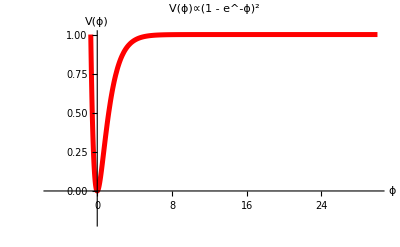

```mathematica
Plot[(1-Exp[-x])^2,{x,-5,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->{Red,Thickness[0.009]},PlotLabel->"V(ϕ)∝(1 - e^-ϕ)^2",PlotRange->{-0.2,1}]
```

### We want the potential to be constant for -ϕ , so I’m going to reflect the function over the y-axis by changing the exponent to +ϕ ,

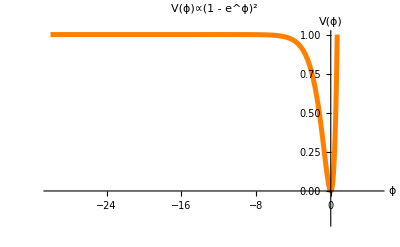

```mathematica
Plot[(1-Exp[x])^2,{x,-30,5},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->{Orange,Thickness[0.009]},PlotLabel->"V(ϕ)∝(1 - e^ϕ)^2",PlotRange->{-0.2,1}]
```

### Now I’m going to make the function less simplistic by including the -sqrt(2/3) term and dividing by the Planck mass in micrograms,

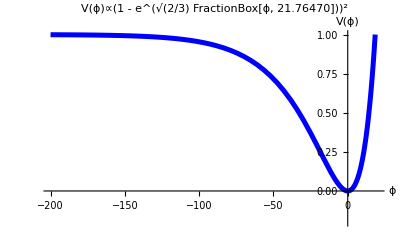

```mathematica
Plot[(1-Exp[(√(2/3))x/(21.76470)])^2,{x,-200,20},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->{Blue,Thickness[0.009]},PlotLabel->"V(ϕ)∝(1 - e^(√(2/3) FractionBox[ϕ, 21.76470]))^2",PlotRange->{-0.2,1}]
```

```mathematica
(* The plot is now more "squished" down vs the previous one which was very stretched up *)
```

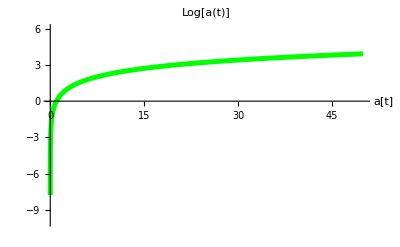

```mathematica
Plot[Log[a[t]],{a[t],-10,50},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"a[t]"},PlotStyle->{Green,Thickness[0.009]},PlotLabel->"Log[a(t)]",PlotRange->{-10,6}]
```